```mathematica
SetDirectory[NotebookDirectory[]];
RPMs={1300,1550,1800,2100,2500};
pressure[1]=Sort[Import["Fan_1330.dat"]];
pressure[2]=Sort[Import["Fan_1550.dat"]];
pressure[3]=Sort[Import["Fan_1800.dat"]];
pressure[4]=Sort[Import["Fan_2100.dat"]];
pressure[5]=Sort[Import["Fan_2500.dat"]];
power[1]=Sort[Import["Power_1330.dat"]];
power[2]=Sort[Import["Power_1550.dat"]];
power[3]=Sort[Import["Power_1800.dat"]];
power[4]=Sort[Import["Power_2100.dat"]];
power[5]=Sort[Import["Power_2500.dat"]];
fpressure[i_,x_]:=Interpolation[pressure[i]][x]
fpower[i_,x_]:=Interpolation[power[i]][x]
feff[i_,x_]:=If[x<=Min[pressure[i][[-1,1]],power[i][[-1,1]]],If[x>Max[pressure[i][[1,1]],power[i][[1,1]]],(x fpressure[i,x]248.84 0.00047194745)/fpower[i,x],0],0]
ShiftData[list_,V_,Vref_]:=Table[{list[[i,1]] V/Vref,list[[i,2]](V/Vref)^2},{i,1,Length[list]}]
ShiftDataPower[list_,V_,Vref_]:=Table[{list[[i,1]] V/Vref,list[[i,2]](V/Vref)^3},{i,1,Length[list]}]
fshift[list_,V_,Vref_,Q_]:=Interpolation[ShiftData[list,V,Vref]][Q]
fshiftpower[list_,V_,Vref_,Q_]:=Interpolation[ShiftDataPower[list,V,Vref]][Q]
```

```mathematica
Z=10^-5;
Manipulate[Show[ListPlot[{pressure[1],pressure[2],pressure[3],pressure[4],pressure[5],ShiftData[pressure[i],RPM0,RPMs[[i]]]},PlotRange->{{0,310},{0,0.8}},Joined->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [inH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[Append[RPMs,RPM0],Scaled[{0.6,0.8}]]],Plot[Z Q^2,{Q,0,1000},PlotStyle->{Black,Dashed}]],{i,1,Length[RPMs],1},{{RPM0,RPMs[[i]]},RPMs[[1]],RPMs[[-1]]}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partd: Part specification RPMs[[1]] is longer than depth of object.

Append::normal: 
   Nonatomic expression expected at position 1 in Append[RPMs, 2000].

```mathematica
Z=10^-5;
Manipulate[ListPlot[{power[1],power[2],power[3],power[4],power[5],ShiftDataPower[power[i],RPM0,RPMs[[i]]]},PlotRange->{{0,310},{0,32}},Joined->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Power [W]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[Append[RPMs,RPM0],Scaled[{0.6,0.85}]]],{i,1,Length[RPMs],1},{{RPM0,RPMs[[i]]},RPMs[[1]],RPMs[[-1]]}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

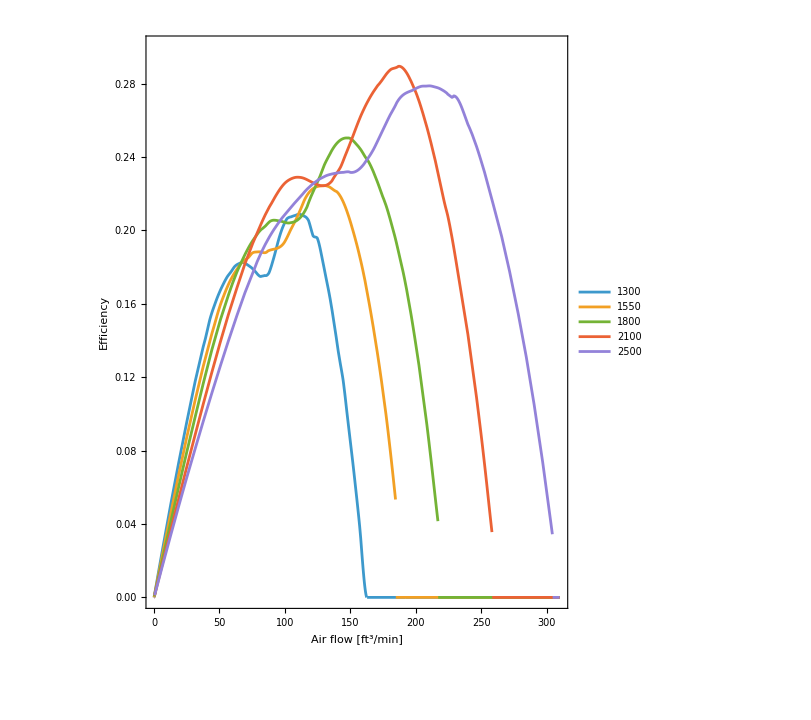

```mathematica
Plot[{feff[1,x],feff[2,x],feff[3,x],feff[4,x],feff[5,x]},{x,0,310},PlotRange->{{0,310},{0,0.3}},AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Efficiency"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[RPMs,Scaled[{0.1,0.8}]]]
```

```mathematica
(*Jacob's measurement*)
```

```mathematica
powers={2.345,4.4775,7.1,10.2625,13.65,15.741,17.901,19.7258,21.0864};
CFMs={101.1,132.5,160.4,180.2,198.4,205.1,213,226.6,227};
tab=Table[{CFMs[[i]],powers[[i]]},{i,1,Length[powers]}];
Manipulate[Show[ListPlot[tab,PlotRange->{{0,230},{0,25}},Frame->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Power [W]"},FrameStyle->Directive[Black,18],ImageSize->600],Plot[a x^3,{x,0,250},PlotStyle->Black]],{{a,1.85 10^-6},0,10^-4}]
```

ListPlot::lpn: tab is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[tab,PlotRange→{{0,230},{0,25}},Frame→True,AspectRatio→1.2,Frame→True,FrameLabel→{Air flow [ft^3/min],Power [W]},FrameStyle→Directive[color,18],ImageSize→600],].

```mathematica
Z=10^-5;
Manipulate[Show[ListPlot[ShiftData[pressure[i],RPM0,RPMs[[i]]],PlotRange->{{0,310},{0,0.8}},Joined->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [inH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600],Plot[Z Q^2,{Q,0,1000},PlotStyle->{Black,Dashed}]],{i,1,Length[RPMs],1},{{RPM0,RPMs[[i]]},RPMs[[1]],RPMs[[-1]]}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
fshift[pressure[1],V,1330][100]
```

fshift[{{-0.173081,0.265498},{3.09782,0.259366},{6.39041,0.252058},{9.68299,0.24475},{12.9761,0.237902},{16.2683,0.230249},{19.5627,0.224449},{22.8563,0.217971},{26.1502,0.211755},{29.4444,0.205825},{32.7382,0.199518},{36.0323,0.193523},{39.5162,0.184848},{42.6188,0.179985},{45.9102,0.171673},{49.2012,0.163109},{52.4922,0.154439},{55.7827,0.145427},{58.2657,0.138702},{61.4669,0.130297},{64.7567,0.120642},{68.0467,0.111209},{71.3368,0.101817},{74.6278,0.0931877},{77.9197,0.0853135},{81.2132,0.0787308},{84.51,0.0749653},{87.7784,0.0725011},{91.1102,0.0729249},{94.7137,0.07457},{98.0165,0.0758451},{101.618,0.0759086},{104.917,0.0741757},{108.217,0.0724803},{111.606,0.0709567},{114.815,0.0688434},{118.083,0.066203},{121.548,0.0617551},{124.708,0.0595078},{128.003,0.0546277},{131.298,0.0491742},{134.593,0.0439832},{137.888,0.0384722},{141.183,0.0330597},{144.479,0.0284759},{147.773,0.0227434},{151.068,0.017536},{154.363,0.012345},{157.658,0.00721971},{161.078,0.00119799},{163.352,-4.85155×10^-7}},1330.,1330][100]

```mathematica
Manipulate[Show[Plot[fshift[pressure[1],V,1330,Q],{Q,0,310},PlotRange->{0,0.8},AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [inH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600],Plot[Z Q^2,{Q,0,1000},PlotStyle->{Black,Dashed}]],{i,1,Length[RPMs],1},{{V,1330.},1330.,2500.}]
```

```mathematica
Manipulate[Show[Plot[fshiftpower[power[1],V,1330,Q],{Q,0,310},PlotRange->{0,35},AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [inH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600],Plot[Z Q^2,{Q,0,1000},PlotStyle->{Black,Dashed}]],{i,1,Length[RPMs],1},{{V,1330.},1330.,2500.}]
```

```mathematica
Z=10^-5;
tt=Table[{V,Q/.FindRoot[fshift[pressure[1],V,1330,Q]-Z Q^2,{Q,0}],fshiftpower[power[1],V,1330,Q/.FindRoot[fshift[pressure[1],V,1330,Q]-Z Q^2,{Q,0}]]},{V,1330.,2500.,10}];
Z=3.7 10^-5;
tt2=Table[{V,Q/.FindRoot[fshift[pressure[1],V,1330,Q]-Z Q^2,{Q,0}],fshiftpower[power[1],V,1330,Q/.FindRoot[fshift[pressure[1],V,1330,Q]-Z Q^2,{Q,0}]]},{V,1330.,2500.,10}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

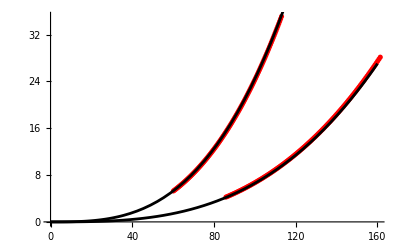

```mathematica
Show[ListPlot[{tt[[All,{2,3}]],tt2[[All,{2,3}]]},PlotRange->{{0,160},All},PlotStyle->Red],Plot[{6.6 10^-6 x^3,3.7 6.6 10^-6 x^3},{x,0,160},PlotStyle->Black]]
```

```mathematica
(*Curve where you can vary the voltage for a given load and see that you are able to optimize efficiency*)
(*Impact of sink-hotspot distance*)
(*Is it possible to extract Z from SimScale*)
(*Try Surface data extraction from SimScale*)
```